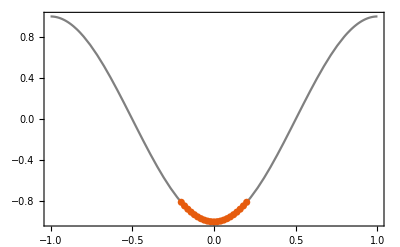

-19.5126

```mathematica
L=100;nkF = 10;
ks = Table[(2π)/L nk, {nk, -nkF,nkF}];
spectrumPlot= Plot[-Cos[π k],{k,-1,1},PlotTheme->"Scientific",PlotStyle->Gray];
occupiedModesPlot=ListPlot[occupiedModes={ks/π,-Cos[ks]}ᵀ,PlotTheme->"Scientific"];
<<MaTeX`
Show[spectrumPlot,occupiedModesPlot,FrameLabel->MaTeX[{"k/\\pi","E_0"}],GridLines->{2/L nkF{-1,+1},None}]
Total[occupiedModes[[;;,2]]]//N
```

```mathematica
Sum[-Cos[(2π)/el nk],{nk,-nkf,nkf}]//FullSimplify
```

-Csc[π/el] Sin[(π+2 nkf π)/el]